## With spaces

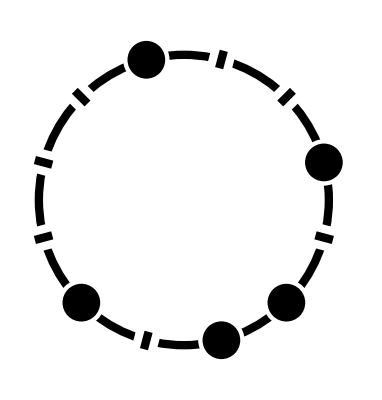

```mathematica
complementaryNoteList[l_]:=Complement[Range[12],l]
radialLine[p_,innerRadius_]:={Line[{Normalize[p]/innerRadius,Normalize[p]*innerRadius}]}
whiteDotLineThickness = 0.01;
blackDotRadius = 0.13;
lineThickness = 0.015;
circle1[centre_:{0,0},radius_:1] := {Thickness->lineThickness,Circle[centre,radius]}
ringFromNoteList[l_]:= Graphics[{circle1[],{White,Disk[#,blackDotRadius+2lineThickness]&/@ CirclePoints[12][[l]]},{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},
{{White,Thickness->lineThickness*3,radialLine[#,0.94]}&/@ CirclePoints[12][[complementaryNoteList[l]]]},{{Thickness->lineThickness,radialLine[#,0.94]}&/@ CirclePoints[12][[complementaryNoteList[l]]]}}
]
ringFromNoteList[{1,2,4,7,11}]
```

## Without spaces

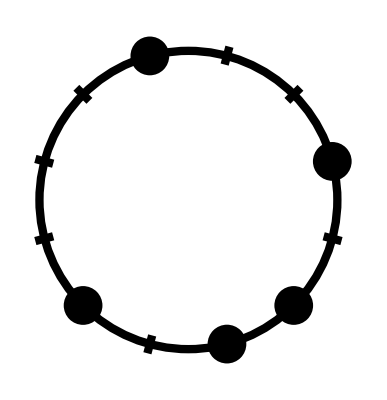

```mathematica
complementaryNoteList[l_]:=Complement[Range[12],l]
radialLine[p_,innerRadius_]:={Line[{Normalize[p]/innerRadius,Normalize[p]*innerRadius}]}
whiteDotLineThickness = 0.01;
blackDotRadius = 0.13;
lineThickness = 0.015;
circle1[centre_:{0,0},radius_:1] := {Thickness->lineThickness,Circle[centre,radius]}
ringFromNoteList[l_]:= Graphics[{circle1[],{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},
{{Thickness->lineThickness,radialLine[#,0.94]}&/@ CirclePoints[12][[complementaryNoteList[l]]]}}
]
ringFromNoteList[{1,2,4,7,11}]
```

## Ticks on the inside only

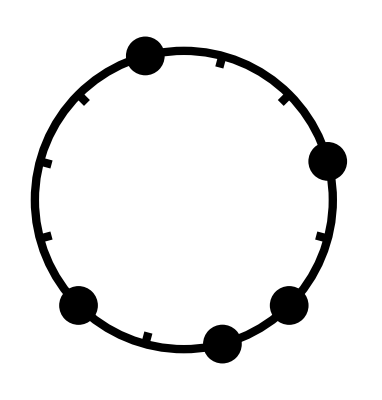

```mathematica
complementaryNoteList[l_]:=Complement[Range[12],l]
radialLine[p_,innerRadius_]:={Line[{Normalize[p]*innerRadius,Normalize[p]}]}
whiteDotLineThickness = 0.01;
blackDotRadius = 0.13;
lineThickness = 0.015;
circle1[centre_:{0,0},radius_:1] := {Thickness->lineThickness,Circle[centre,radius]}
ringFromNoteList[l_]:= Graphics[{circle1[],{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},
{{Thickness->lineThickness,radialLine[#,0.92]}&/@ CirclePoints[12][[complementaryNoteList[l]]]}}
]
ringFromNoteList[{1,2,4,7,11}]
```

## With inside ticks and spaces

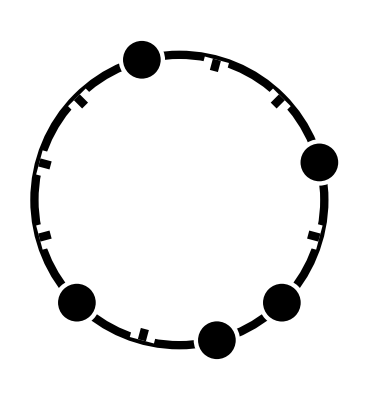

```mathematica
complementaryNoteList[l_]:=Complement[Range[12],l]
radialLine[p_,innerRadius_]:={Line[{Normalize[p],Normalize[p]*innerRadius}]}
whiteDotLineThickness = 0.01;
blackDotRadius = 0.13;
lineThickness = 0.015;
circle1[centre_:{0,0},radius_:1] := {Thickness->lineThickness,Circle[centre,radius]}
ringFromNoteList[l_]:= Graphics[{circle1[],{White,Disk[#,blackDotRadius+2lineThickness]&/@ CirclePoints[12][[l]]},{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},
{{White,Thickness->lineThickness*3,radialLine[#,0.92]}&/@ CirclePoints[12][[complementaryNoteList[l]]]},{{Thickness->lineThickness,radialLine[#,0.92]}&/@ CirclePoints[12][[complementaryNoteList[l]]]}}
]
ringFromNoteList[{1,2,4,7,11}]
```

## Small empty circles instead of ticks

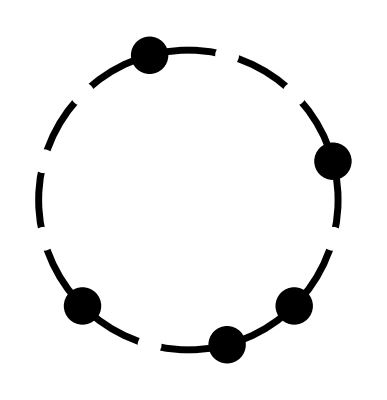

```mathematica
whiteDotLineThickness = 0.01;
blackDotRadius = 0.125;
whiteDotRadius = blackDotRadius * 0.45;
lineThickness = 0.0125;
ringFromNoteList[l_]:= Graphics[{circle1[],{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},{White,EdgeForm[Thickness[lineThickness]],Disk[#,whiteDotRadius]&/@ CirclePoints[12][[complementaryNoteList[l]]]}}]
ringFromNoteList[{1,2,4,7,11}]
```

## Small empty circles with spaces

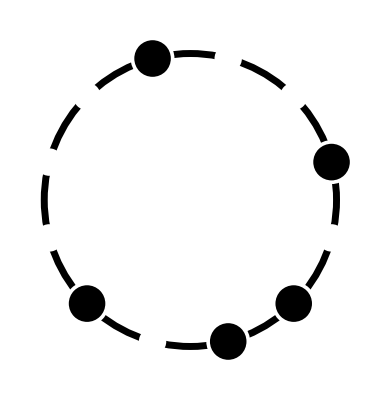

```mathematica
whiteDotLineThickness = 0.01;
blackDotRadius = 0.125;
whiteDotRadius = blackDotRadius * 0.45;
lineThickness = 0.0125;
ringFromNoteList[l_]:= Graphics[{circle1[],{White,Disk[#,blackDotRadius+2lineThickness]&/@ CirclePoints[12][[l]]},
{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},
{White,Disk[#,whiteDotRadius+3*lineThickness]&/@ CirclePoints[12][[complementaryNoteList[l]]]},{White,EdgeForm[Thickness[lineThickness]],Disk[#,whiteDotRadius]&/@ CirclePoints[12][[complementaryNoteList[l]]]}}]
ringFromNoteList[{1,2,4,7,11}]
```

## Older ideas

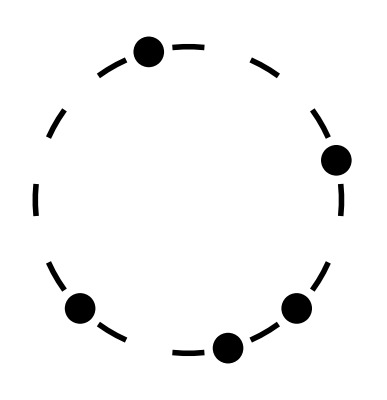

```mathematica
circle12[centre_:{0,0},radius_:1] := {Thickness->0.01,Circle[centre,radius, #]}&/@Table[π/6{(n + 1 - 0.2),(n + 1 + 0.2)},{n,1,12}]
ringFromNoteList[l_]:= Graphics[{Disk[#,0.1]&/@ CirclePoints[12][[l]],circle12[]}]
ringFromNoteList[{1,2,4,7,11}]
```

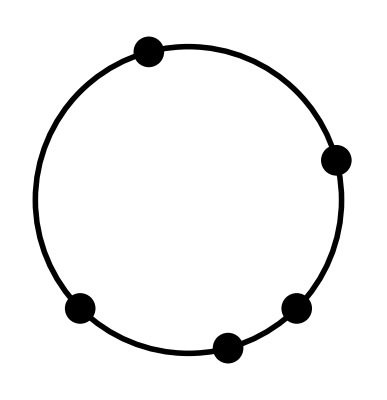

```mathematica
circle0[centre_:{0,0},radius_:1] := {Thickness->0.01,Circle[centre,radius]}
ringFromNoteList[l_]:= Graphics[{Disk[#,0.1]&/@ CirclePoints[12][[l]],circle0[]}]
ringFromNoteList[{1,2,4,7,11}]
```

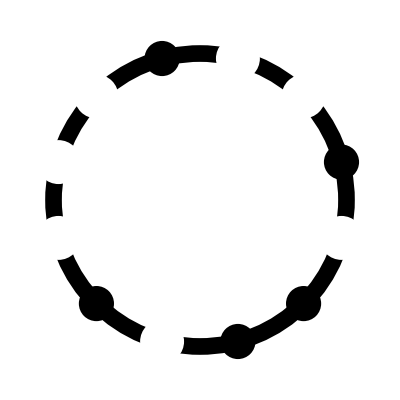

```mathematica
circle0[centre_:{0,0},radius_:1] := {Thickness->0.03,Circle[centre,radius]}
complementaryNoteList[l_]:=Complement[Range[12],l]
ringFromNoteList[l_]:= Graphics[{{Black,Disk[#,0.12]&/@ CirclePoints[12][[l]]},circle0[],{White,Disk[#,0.15]&/@ CirclePoints[12][[complementaryNoteList[l]]]}}]
ringFromNoteList[{1,2,4,7,11}]
```

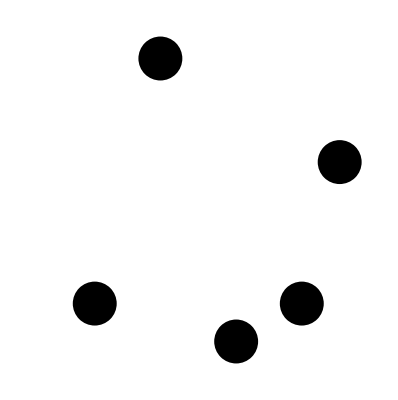

```mathematica
whiteDotLineThickness = 0.01;
blackDotRadius = 0.15;
whiteDotRadius = blackDotRadius - whiteDotLineThickness;
ringFromNoteList[l_]:= Graphics[{{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},{White,EdgeForm[Thickness[whiteDotLineThickness]],Disk[#,whiteDotRadius]&/@ CirclePoints[12][[complementaryNoteList[l]]]}}]
ringFromNoteList[{1,2,4,7,11}]
```

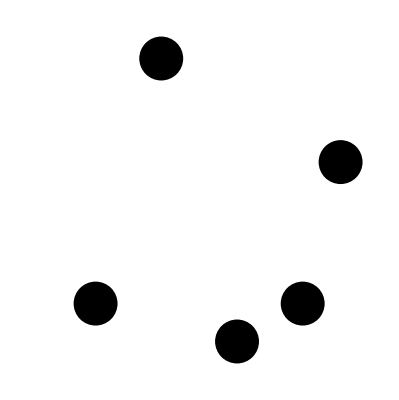

```mathematica
whiteDotLineThickness = 0.005;
blackDotRadius = 0.15;
whiteDotRadius = blackDotRadius - whiteDotLineThickness;
ringFromNoteList[l_]:= Graphics[{{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},{White,EdgeForm[Thickness[whiteDotLineThickness]],Disk[#,whiteDotRadius]&/@ CirclePoints[12][[complementaryNoteList[l]]]}}]
ringFromNoteList[{1,2,4,7,11}]
```

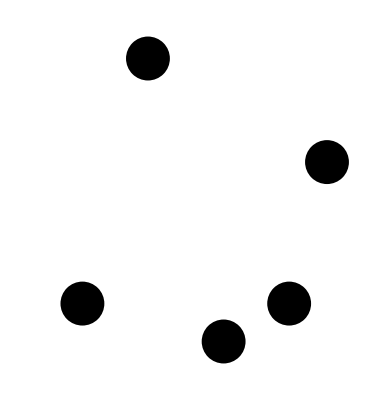

```mathematica
whiteDotLineThickness = 0.01;
blackDotRadius = 0.15;
whiteDotRadius = 0.065;
ringFromNoteList[l_]:= Graphics[{{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},{White,EdgeForm[Thickness[whiteDotLineThickness]],Disk[#,whiteDotRadius]&/@ CirclePoints[12][[complementaryNoteList[l]]]}}]
ringFromNoteList[{1,2,4,7,11}]
```

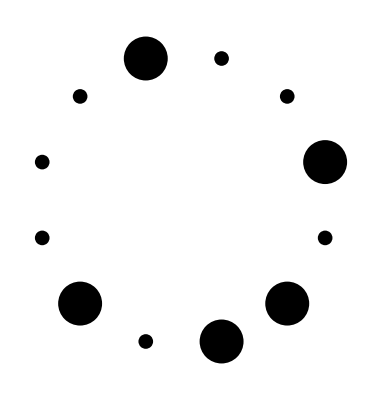

```mathematica
whiteDotLineThickness = 0.01;
blackDotRadius = 0.15;
whiteDotRadius = 0.05;
ringFromNoteList[l_]:= Graphics[{{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},{Black,Disk[#,whiteDotRadius]&/@ CirclePoints[12][[complementaryNoteList[l]]]}}]
ringFromNoteList[{1,2,4,7,11}]
```

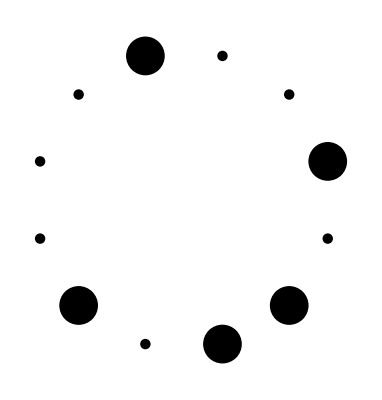

```mathematica
whiteDotLineThickness = 0.01;
blackDotRadius = 0.13;
whiteDotRadius = 0.035;
ringFromNoteList[l_]:= Graphics[{{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},{Black,Disk[#,whiteDotRadius]&/@ CirclePoints[12][[complementaryNoteList[l]]]}}]
ringFromNoteList[{1,2,4,7,11}]
```

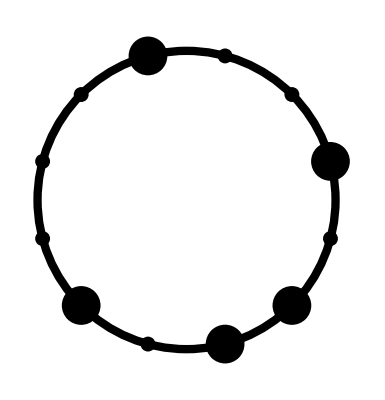

```mathematica
whiteDotLineThickness = 0.01;
blackDotRadius = 0.13;
whiteDotRadius = 0.05;
circle1[centre_:{0,0},radius_:1] := {Thickness->0.015,Circle[centre,radius]}
ringFromNoteList[l_]:= Graphics[{{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},{Black,Disk[#,whiteDotRadius]&/@ CirclePoints[12][[complementaryNoteList[l]]]},circle1[]}]
ringFromNoteList[{1,2,4,7,11}]
```

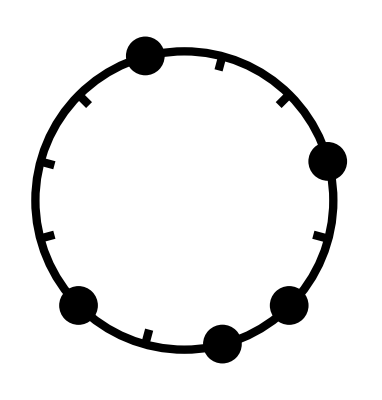

```mathematica
radialLine[p_,innerRadius_]:={Line[{p,Normalize[p]*innerRadius}]}
whiteDotLineThickness = 0.01;
blackDotRadius = 0.13;
lineThickness = 0.015;
circle1[centre_:{0,0},radius_:1] := {Thickness->lineThickness,Circle[centre,radius]}
ringFromNoteList[l_]:= Graphics[{{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},{{Thickness->lineThickness,radialLine[#,0.9]}&/@ CirclePoints[12][[complementaryNoteList[l]]]},circle1[]}]
ringFromNoteList[{1,2,4,7,11}]
```

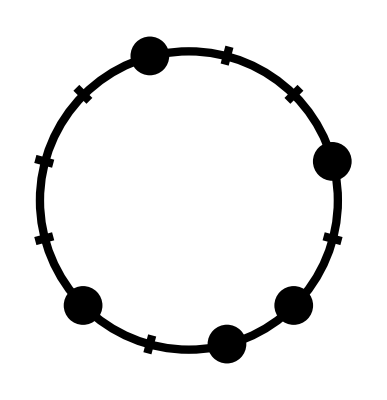

```mathematica
radialLine[p_,innerRadius_]:={Line[{Normalize[p]/innerRadius,Normalize[p]*innerRadius}]}
whiteDotLineThickness = 0.01;
blackDotRadius = 0.13;
lineThickness = 0.015;
circle1[centre_:{0,0},radius_:1] := {Thickness->lineThickness,Circle[centre,radius]}
ringFromNoteList[l_]:= Graphics[{{Black,Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]]},{{Thickness->lineThickness,radialLine[#,0.94]}&/@ CirclePoints[12][[complementaryNoteList[l]]]},circle1[]}]
ringFromNoteList[{1,2,4,7,11}]
```

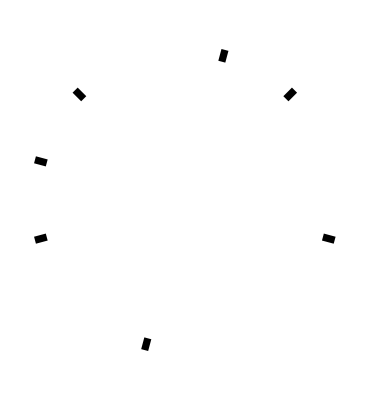

```mathematica
radialLine[p_,innerRadius_]:={Line[{Normalize[p]/innerRadius,Normalize[p]*innerRadius}]}
whiteDotLineThickness = 0.01;
blackDotRadius = 0.13;
lineThickness = 0.013;
circle1[centre_:{0,0},radius_:1] := {Thickness->lineThickness,Circle[centre,radius]}
ringFromNoteList[l_]:= Graphics[{White,EdgeForm[Thickness[whiteDotLineThickness]],Disk[#,blackDotRadius]&/@ CirclePoints[12][[l]],{{Black,Thickness->lineThickness,radialLine[#,0.96]}&/@ CirclePoints[12][[complementaryNoteList[l]]]}}]
ringFromNoteList[{1,2,4,7,11}]
```

```mathematica
Graphics[{{{EdgeForm[Thickness[0.01]],Black,Annulus[{0,0},{0.7,1},{#,#+2π/12}]}&/@(2π Range[12]/12)[[{1,2,4,7,11}]]},
{EdgeForm[Thickness[0.01]],White,Annulus[{0,0},{0.7,1},{#,#+2π/12}]}&/@(2π Range[12]/12)[[complementaryNoteList[{1,2,4,7,11}]]]}]
```

-Graphics-

```mathematica
Graphics[{{{EdgeForm[{White,Thickness[0.01]}],Black,Annulus[{0,0},{0.78,1.02},{#,#+2π/12}]}&/@(2π Range[12]/12)[[{1,2,4,7,11}]]},
{EdgeForm[Thickness[0.01]],White,Annulus[{0,0},{0.8,1},{#,#+2π/12}]}&/@(2π Range[12]/12)[[complementaryNoteList[{1,2,4,7,11}]]]}]
```

-Graphics-

```mathematica
Graphics[{{{EdgeForm[Thickness[0.01]],Black,Annulus[{0,0},{0.2,1},{#,#+2π/12}]}&/@(2π Range[12]/12)[[{1,2,4,7,11}]]},
{EdgeForm[Thickness[0.01]],White,Annulus[{0,0},{0.2,1},{#,#+2π/12}]}&/@(2π Range[12]/12)[[complementaryNoteList[{1,2,4,7,11}]]]}]
```

-Graphics-

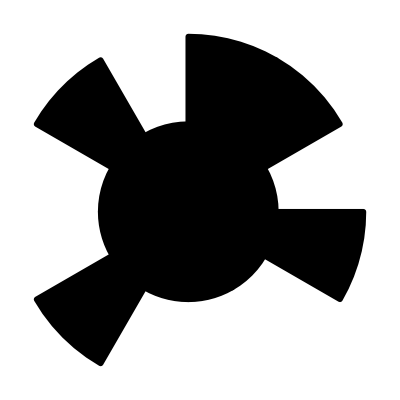

```mathematica
Graphics[{{{EdgeForm[Thickness[0.01]],Black,Disk[{0,0},1,{#,#+2π/12}]}&/@(2π Range[12]/12)[[{1,2,4,7,11}]]},
{EdgeForm[Thickness[0.01]],Black,Disk[{0,0},0.5,{#,#+2π/12}]}&/@(2π Range[12]/12)[[complementaryNoteList[{1,2,4,7,11}]]]}]
```

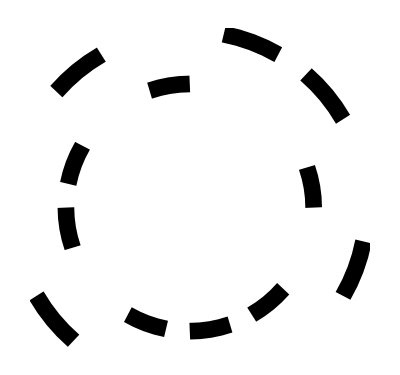

```mathematica
Graphics[{{{Thickness[0.03],Black,Circle[{0,0},1,{#,#+2π/19}]}&/@(2π Range[12]/12)[[{1,2,4,7,11}]]},
{Thickness[0.03],Black,Circle[{0,0},0.7,{#,#+2π/19}]}&/@(2π Range[12]/12)[[complementaryNoteList[{1,2,4,7,11}]]]}]
```